```mathematica
Clear[w1N,w2N,w3N,mu1N,mu1Half,mu2N,mu2Half,mu2Full,mu3N,mu3Half,f,ϵ]
```

```mathematica
(*This sheet shows that TH(w1,w2,w3)≠TH(w3,w2,w1) particularly if w1>w3 TH(w1,w2,w3)>TH(w3,w2,w1)*)
mu1N:=1/w1N
mu1Half:=1/(w1N-f w1N/2)
mu2N:=1
mu2Half:=1/(1-f/2)
mu2Full:=1/(1-f)
mu3N:=1/w3N
mu3Half:=1/(w3N-f w3N/2)
```

```mathematica
𝒫:=ContinuousMarkovProcess[1,({{-mu1Half, mu1Half, 0, 0, 0, 0, 0, 0}, {0, -mu1N-mu2Half, mu1N, mu2Half, 0, 0, 0, 0}, {0, 0, -mu2Full, 0, mu2Full, 0, 0, 0}, {mu3N, 0, 0, -mu1Half-mu3N, mu1Half, 0, 0, 0}, {0, mu3N, 0, 0, -mu1N-mu2N-mu3N, mu1N, mu2N, 0}, {0, 0, mu3N, 0, 0, -mu2Half-mu3N, 0, mu2Half}, {0, 0, 0, mu3Half, 0, 0, -mu1N-mu3Half, mu1N}, {0, 0, 0, 0, mu3Half, 0, 0, -mu3Half}})]
```

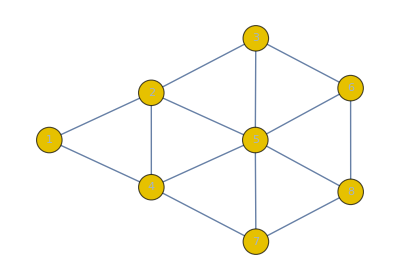

```mathematica
Graph[𝒫]
```

```mathematica
Clear[w1N,w2N,w3N,f]
```

```mathematica
TH:=(∑_(i=4)^6 PDF[𝒫[∞],i])mu3N+(∑_(i=7)^8 PDF[𝒫[∞],i])mu3Half
```

```mathematica
THSimple[f_,w1N_,w3N_]:=-((2 (f-2 (1+w3N)) (-2 (-2+f)^2 w3N^3+4 (-2+f) w1N^4 (1+w3N)+(-2+f) w1N w3N^2 (12+f^2+8 w3N-2 f (3+w3N))-2 w1N^3 (-4 f (1+3 w3N)+f^2 (1+3 w3N)+4 (1+4 w3N+w3N^2))+w1N^2 w3N (f^3 (1+w3N)-2 f^2 (4+3 w3N)-8 (3+4 w3N+w3N^2)+4 f (6+5 w3N+w3N^2))))/(-4 (-2+f)^3 w3N^3 (-1+f-w3N-w3N^2)+4 (-2+f)^2 w1N^5 (1+w3N) (f-2 (1+w3N))-4 (-2+f) w1N^4 (f^3 w3N-f^2 (1+7 w3N+2 w3N^2)+4 f (1+5 w3N+3 w3N^2)-4 (1+5 w3N+5 w3N^2+w3N^3))+2 (-2+f)^2 w1N w3N^2 (f^3-f^2 (7+w3N+2 w3N^2)+2 f (9+7 w3N+4 w3N^2+w3N^3)-4 (3+5 w3N+5 w3N^2+2 w3N^3))+(-2+f) w1N^2 w3N (f^4 (2+w3N^2)-2 f^3 (9+3 w3N+4 w3N^2+w3N^3)+4 f^2 (16+10 w3N+9 w3N^2+4 w3N^3)+16 (3+7 w3N+8 w3N^2+5 w3N^3+w3N^4)-8 f (12+16 w3N+12 w3N^2+6 w3N^3+w3N^4))-2 w1N^3 (12 f^2 (1+w3N)^2 (3+2 w3N)+16 (1+w3N)^2 (1+3 w3N+w3N^2)+f^4 (2+3 w3N+w3N^2)-2 f^3 (7+14 w3N+9 w3N^2+w3N^3)-8 f (5+18 w3N+21 w3N^2+9 w3N^3+w3N^4))))
```

```mathematica
TH1:=THSimple[f,1+ϵ,1]
TH2:=THSimple[f,1,1+ϵ]
```

```mathematica
FullSimplify[TH1-TH2]
```

-((2 (-2+f) f ϵ (1+ϵ) (f-2 (2+ϵ)) (f^6 (1+ϵ)^2 (3+2 ϵ)-64 (2+ϵ) (3+2 ϵ)^3-2 f^5 (1+ϵ) (5+4 ϵ) (5+ϵ (5+ϵ))+4 f^4 (1+ϵ) (82+ϵ (164+ϵ (113+2 ϵ (15+ϵ))))-32 f (-59+2 ϵ (-43+ϵ (4+ϵ (37+22 ϵ+4 ϵ^2))))+16 f^2 (52+ϵ (259+2 ϵ (213+ϵ (161+58 ϵ+8 ϵ^2))))-8 f^3 (122+ϵ (410+ϵ (525+2 ϵ (161+ϵ (47+5 ϵ)))))))/((f^5 (1+ϵ) (5+3 ϵ)-32 (2+ϵ) (39+4 ϵ (19+ϵ (15+ϵ (6+ϵ))))-4 f^4 (22+ϵ (40+ϵ (25+ϵ (7+ϵ))))+16 f (227+ϵ (525+ϵ (513+2 ϵ (137+5 ϵ (8+ϵ)))))+4 f^3 (153+ϵ (306+ϵ (241+ϵ (99+2 ϵ (11+ϵ)))))-8 f^2 (264+ϵ (571+2 ϵ (257+2 ϵ (63+ϵ (17+2 ϵ)))))) (f^5 (1+ϵ) (5+ϵ (4+ϵ))-32 (2+ϵ) (39+4 ϵ (19+ϵ (15+ϵ (6+ϵ))))-2 f^4 (44+ϵ (82+ϵ (57+ϵ (20+3 ϵ))))+4 f^3 (153+ϵ (303+ϵ (243+2 ϵ (53+ϵ (12+ϵ)))))-8 f^2 (264+ϵ (561+4 ϵ (125+ϵ (62+ϵ (17+2 ϵ)))))+16 f (227+ϵ (519+ϵ (502+ϵ (268+ϵ (79+10 ϵ))))))))

```mathematica
Numerator[%35]
```

-2 (-2+f) f ϵ (1+ϵ) (f-2 (2+ϵ)) (f^6 (1+ϵ)^2 (3+2 ϵ)-64 (2+ϵ) (3+2 ϵ)^3-2 f^5 (1+ϵ) (5+4 ϵ) (5+ϵ (5+ϵ))+4 f^4 (1+ϵ) (82+ϵ (164+ϵ (113+2 ϵ (15+ϵ))))-32 f (-59+2 ϵ (-43+ϵ (4+ϵ (37+22 ϵ+4 ϵ^2))))+16 f^2 (52+ϵ (259+2 ϵ (213+ϵ (161+58 ϵ+8 ϵ^2))))-8 f^3 (122+ϵ (410+ϵ (525+2 ϵ (161+ϵ (47+5 ϵ))))))

```mathematica
Expand[%36]
```

55296 f ϵ-71680 f^2 ϵ+16256 f^3 ϵ+21824 f^4 ϵ-18624 f^5 ϵ+6688 f^6 ϵ-1304 f^7 ϵ+136 f^8 ϵ-6 f^9 ϵ+221184 f ϵ^2-248320 f^2 ϵ^2+1152 f^3 ϵ^2+129664 f^4 ϵ^2-88544 f^5 ϵ^2+29008 f^6 ϵ^2-5304 f^7 ϵ^2+524 f^8 ϵ^2-22 f^9 ϵ^2+364032 f ϵ^3-325888 f^2 ϵ^3-133248 f^3 ϵ^3+300160 f^4 ϵ^3-172672 f^5 ϵ^3+51312 f^6 ϵ^3-8632 f^7 ϵ^3+784 f^8 ϵ^3-30 f^9 ϵ^3+315904 f ϵ^4-181504 f^2 ϵ^4-277888 f^3 ϵ^4+360960 f^4 ϵ^4-178784 f^5 ϵ^4+47488 f^6 ϵ^4-7120 f^7 ϵ^4+564 f^8 ϵ^4-18 f^9 ϵ^4+152576 f ϵ^5-10240 f^2 ϵ^5-256000 f^3 ϵ^5+246976 f^4 ϵ^5-105696 f^5 ϵ^5+24416 f^6 ϵ^5-3088 f^7 ϵ^5+192 f^8 ϵ^5-4 f^9 ϵ^5+38912 f ϵ^6+35328 f^2 ϵ^6-123904 f^3 ϵ^6+96640 f^4 ϵ^6-35296 f^5 ϵ^6+6752 f^6 ϵ^6-648 f^7 ϵ^6+24 f^8 ϵ^6+4096 f ϵ^7+15360 f^2 ϵ^7-30720 f^3 ϵ^7+19968 f^4 ϵ^7-6016 f^5 ϵ^7+864 f^6 ϵ^7-48 f^7 ϵ^7+2048 f^2 ϵ^8-3072 f^3 ϵ^8+1664 f^4 ϵ^8-384 f^5 ϵ^8+32 f^6 ϵ^8

```mathematica
Collect[%37,f]
```

f^9 (-6 ϵ-22 ϵ^2-30 ϵ^3-18 ϵ^4-4 ϵ^5)+f^8 (136 ϵ+524 ϵ^2+784 ϵ^3+564 ϵ^4+192 ϵ^5+24 ϵ^6)+f^7 (-1304 ϵ-5304 ϵ^2-8632 ϵ^3-7120 ϵ^4-3088 ϵ^5-648 ϵ^6-48 ϵ^7)+f (55296 ϵ+221184 ϵ^2+364032 ϵ^3+315904 ϵ^4+152576 ϵ^5+38912 ϵ^6+4096 ϵ^7)+f^3 (16256 ϵ+1152 ϵ^2-133248 ϵ^3-277888 ϵ^4-256000 ϵ^5-123904 ϵ^6-30720 ϵ^7-3072 ϵ^8)+f^5 (-18624 ϵ-88544 ϵ^2-172672 ϵ^3-178784 ϵ^4-105696 ϵ^5-35296 ϵ^6-6016 ϵ^7-384 ϵ^8)+f^6 (6688 ϵ+29008 ϵ^2+51312 ϵ^3+47488 ϵ^4+24416 ϵ^5+6752 ϵ^6+864 ϵ^7+32 ϵ^8)+f^4 (21824 ϵ+129664 ϵ^2+300160 ϵ^3+360960 ϵ^4+246976 ϵ^5+96640 ϵ^6+19968 ϵ^7+1664 ϵ^8)+f^2 (-71680 ϵ-248320 ϵ^2-325888 ϵ^3-181504 ϵ^4-10240 ϵ^5+35328 ϵ^6+15360 ϵ^7+2048 ϵ^8)

```mathematica
Numerator[%20]
```

-2 (-2+f) f ϵ (1+ϵ) (f-2 (2+ϵ)) (f^6 (1+ϵ)^2 (3+2 ϵ)-64 (2+ϵ) (3+2 ϵ)^3-2 f^5 (1+ϵ) (5+4 ϵ) (5+ϵ (5+ϵ))+4 f^4 (1+ϵ) (82+ϵ (164+ϵ (113+2 ϵ (15+ϵ))))-32 f (-59+2 ϵ (-43+ϵ (4+ϵ (37+22 ϵ+4 ϵ^2))))+16 f^2 (52+ϵ (259+2 ϵ (213+ϵ (161+58 ϵ+8 ϵ^2))))-8 f^3 (122+ϵ (410+ϵ (525+2 ϵ (161+ϵ (47+5 ϵ))))))

```mathematica
Factor[%21]
```

-2 (-2+f) f (-4+f-2 ϵ) ϵ (1+ϵ) (-3456+1888 f+832 f^2-976 f^3+328 f^4-50 f^5+3 f^6-8640 ϵ+2752 f ϵ+4144 f^2 ϵ-3280 f^3 ϵ+984 f^4 ϵ-140 f^5 ϵ+8 f^6 ϵ-8064 ϵ^2-256 f ϵ^2+6816 f^2 ϵ^2-4200 f^3 ϵ^2+1108 f^4 ϵ^2-140 f^5 ϵ^2+7 f^6 ϵ^2-3328 ϵ^3-2368 f ϵ^3+5152 f^2 ϵ^3-2576 f^3 ϵ^3+572 f^4 ϵ^3-58 f^5 ϵ^3+2 f^6 ϵ^3-512 ϵ^4-1408 f ϵ^4+1856 f^2 ϵ^4-752 f^3 ϵ^4+128 f^4 ϵ^4-8 f^5 ϵ^4-256 f ϵ^5+256 f^2 ϵ^5-80 f^3 ϵ^5+8 f^4 ϵ^5)

```mathematica
n1:=2 (-2+f) f (-4+f-2 ϵ) ϵ (1+ϵ) 
n2:=-(-3456+1888 f+832 f^2-976 f^3+328 f^4-50 f^5+3 f^6-8640 ϵ+2752 f ϵ+4144 f^2 ϵ-3280 f^3 ϵ+984 f^4 ϵ-140 f^5 ϵ+8 f^6 ϵ-8064 ϵ^2-256 f ϵ^2+6816 f^2 ϵ^2-4200 f^3 ϵ^2+1108 f^4 ϵ^2-140 f^5 ϵ^2+7 f^6 ϵ^2-3328 ϵ^3-2368 f ϵ^3+5152 f^2 ϵ^3-2576 f^3 ϵ^3+572 f^4 ϵ^3-58 f^5 ϵ^3+2 f^6 ϵ^3-512 ϵ^4-1408 f ϵ^4+1856 f^2 ϵ^4-752 f^3 ϵ^4+128 f^4 ϵ^4-8 f^5 ϵ^4-256 f ϵ^5+256 f^2 ϵ^5-80 f^3 ϵ^5+8 f^4 ϵ^5)
```

```mathematica
(*let NUM=n1*n2 *)
(*n1>0*)
```

```mathematica
Collect[n2,ϵ]
```

3456-1888 f-832 f^2+976 f^3-328 f^4+50 f^5-3 f^6+(8640-2752 f-4144 f^2+3280 f^3-984 f^4+140 f^5-8 f^6) ϵ+(8064+256 f-6816 f^2+4200 f^3-1108 f^4+140 f^5-7 f^6) ϵ^2+(3328+2368 f-5152 f^2+2576 f^3-572 f^4+58 f^5-2 f^6) ϵ^3+(512+1408 f-1856 f^2+752 f^3-128 f^4+8 f^5) ϵ^4+(256 f-256 f^2+80 f^3-8 f^4) ϵ^5

```mathematica
(*n2>0-->NUM>0*)
```

```mathematica
Denominator[%20]
```

(f^5 (1+ϵ) (5+3 ϵ)-32 (2+ϵ) (39+4 ϵ (19+ϵ (15+ϵ (6+ϵ))))-4 f^4 (22+ϵ (40+ϵ (25+ϵ (7+ϵ))))+16 f (227+ϵ (525+ϵ (513+2 ϵ (137+5 ϵ (8+ϵ)))))+4 f^3 (153+ϵ (306+ϵ (241+ϵ (99+2 ϵ (11+ϵ)))))-8 f^2 (264+ϵ (571+2 ϵ (257+2 ϵ (63+ϵ (17+2 ϵ)))))) (f^5 (1+ϵ) (5+ϵ (4+ϵ))-32 (2+ϵ) (39+4 ϵ (19+ϵ (15+ϵ (6+ϵ))))-2 f^4 (44+ϵ (82+ϵ (57+ϵ (20+3 ϵ))))+4 f^3 (153+ϵ (303+ϵ (243+2 ϵ (53+ϵ (12+ϵ)))))-8 f^2 (264+ϵ (561+4 ϵ (125+ϵ (62+ϵ (17+2 ϵ)))))+16 f (227+ϵ (519+ϵ (502+ϵ (268+ϵ (79+10 ϵ))))))

```mathematica
Factor[%23]
```

(-2496+3632 f-2112 f^2+612 f^3-88 f^4+5 f^5-6112 ϵ+8304 f ϵ-4488 f^2 ϵ+1212 f^3 ϵ-164 f^4 ϵ+9 f^5 ϵ-6272 ϵ^2+8032 f ϵ^2-4000 f^2 ϵ^2+972 f^3 ϵ^2-114 f^4 ϵ^2+5 f^5 ϵ^2-3456 ϵ^3+4288 f ϵ^3-1984 f^2 ϵ^3+424 f^3 ϵ^3-40 f^4 ϵ^3+f^5 ϵ^3-1024 ϵ^4+1264 f ϵ^4-544 f^2 ϵ^4+96 f^3 ϵ^4-6 f^4 ϵ^4-128 ϵ^5+160 f ϵ^5-64 f^2 ϵ^5+8 f^3 ϵ^5) (-2496+3632 f-2112 f^2+612 f^3-88 f^4+5 f^5-6112 ϵ+8400 f ϵ-4568 f^2 ϵ+1224 f^3 ϵ-160 f^4 ϵ+8 f^5 ϵ-6272 ϵ^2+8208 f ϵ^2-4112 f^2 ϵ^2+964 f^3 ϵ^2-100 f^4 ϵ^2+3 f^5 ϵ^2-3456 ϵ^3+4384 f ϵ^3-2016 f^2 ϵ^3+396 f^3 ϵ^3-28 f^4 ϵ^3-1024 ϵ^4+1280 f ϵ^4-544 f^2 ϵ^4+88 f^3 ϵ^4-4 f^4 ϵ^4-128 ϵ^5+160 f ϵ^5-64 f^2 ϵ^5+8 f^3 ϵ^5)

```mathematica
(*Denominatior=a*b*)
a:=-(-2496+3632 f-2112 f^2+612 f^3-88 f^4+5 f^5-6112 ϵ+8304 f ϵ-4488 f^2 ϵ+1212 f^3 ϵ-164 f^4 ϵ+9 f^5 ϵ-6272 ϵ^2+8032 f ϵ^2-4000 f^2 ϵ^2+972 f^3 ϵ^2-114 f^4 ϵ^2+5 f^5 ϵ^2-3456 ϵ^3+4288 f ϵ^3-1984 f^2 ϵ^3+424 f^3 ϵ^3-40 f^4 ϵ^3+f^5 ϵ^3-1024 ϵ^4+1264 f ϵ^4-544 f^2 ϵ^4+96 f^3 ϵ^4-6 f^4 ϵ^4-128 ϵ^5+160 f ϵ^5-64 f^2 ϵ^5+8 f^3 ϵ^5) 
b:=-(-2496+3632 f-2112 f^2+612 f^3-88 f^4+5 f^5-6112 ϵ+8400 f ϵ-4568 f^2 ϵ+1224 f^3 ϵ-160 f^4 ϵ+8 f^5 ϵ-6272 ϵ^2+8208 f ϵ^2-4112 f^2 ϵ^2+964 f^3 ϵ^2-100 f^4 ϵ^2+3 f^5 ϵ^2-3456 ϵ^3+4384 f ϵ^3-2016 f^2 ϵ^3+396 f^3 ϵ^3-28 f^4 ϵ^3-1024 ϵ^4+1280 f ϵ^4-544 f^2 ϵ^4+88 f^3 ϵ^4-4 f^4 ϵ^4-128 ϵ^5+160 f ϵ^5-64 f^2 ϵ^5+8 f^3 ϵ^5)
```

```mathematica
Factor[a-b]
```

-(-2+f) f ϵ (1+ϵ) (48-16 f-2 f^2+f^3+40 ϵ+4 f ϵ-8 f^2 ϵ+f^3 ϵ+8 ϵ^2+4 f ϵ^2-2 f^2 ϵ^2)

```mathematica
(*a-b=x
x=x1*x2*)
x1:=-(-2+f) f ϵ (1+ϵ) 
x2:=(48-16 f-2 f^2+f^3+40 ϵ+4 f ϵ-8 f^2 ϵ+f^3 ϵ+8 ϵ^2+4 f ϵ^2-2 f^2 ϵ^2)
(*We can see x1 and x2 are positive--> x positive*)
(*Denominator=a*b=(x+b)b=b^2+xb, positive if xb>0, we know x>0 from above b>0 sufficient*)
b
```

2496-3632 f+2112 f^2-612 f^3+88 f^4-5 f^5+6112 ϵ-8400 f ϵ+4568 f^2 ϵ-1224 f^3 ϵ+160 f^4 ϵ-8 f^5 ϵ+6272 ϵ^2-8208 f ϵ^2+4112 f^2 ϵ^2-964 f^3 ϵ^2+100 f^4 ϵ^2-3 f^5 ϵ^2+3456 ϵ^3-4384 f ϵ^3+2016 f^2 ϵ^3-396 f^3 ϵ^3+28 f^4 ϵ^3+1024 ϵ^4-1280 f ϵ^4+544 f^2 ϵ^4-88 f^3 ϵ^4+4 f^4 ϵ^4+128 ϵ^5-160 f ϵ^5+64 f^2 ϵ^5-8 f^3 ϵ^5

```mathematica
Collect[%40,ϵ]
```

2496-3632 f+2112 f^2-612 f^3+88 f^4-5 f^5+(6112-8400 f+4568 f^2-1224 f^3+160 f^4-8 f^5) ϵ+(6272-8208 f+4112 f^2-964 f^3+100 f^4-3 f^5) ϵ^2+(3456-4384 f+2016 f^2-396 f^3+28 f^4) ϵ^3+(1024-1280 f+544 f^2-88 f^3+4 f^4) ϵ^4+(128-160 f+64 f^2-8 f^3) ϵ^5

```mathematica
(*b>0*)
```

```mathematica
Plot3D[TH1-TH2,{ϵ,0,1},{f,0,1}]
```

-Graphics3D-

```mathematica
(*SUMMARY_1*)
Assuming[ϵ>=0&&1>=f>=0,FullSimplify[TH1-TH2>0]]
```

f ϵ>0

```mathematica
(*SUMMARY_2*)
```

```mathematica
Assuming[ϵ>0&&f==0,FullSimplify[TH1-TH2==0]]
```

True